### Setup

Note: we use m,c as variables instead of u,v

#### PPE solver

```mathematica
ClearAll@runTwoComponentSim;
Options[runTwoComponentSim]=Join[Options[NDSolve],{"GridPoints"->100,"BC"->"Reflective"}];
runTwoComponentSim[{f_,g_},params_,{mInit_,cInit_},tMax_,opts:OptionsPattern[]]:=First@NDSolve[{D[m[x,t],t]==Dm D[m[x,t],{x,2}]+(f/.{m->m[x,t],c->c[x,t]}),D[c[x,t],t]==Dc D[c[x,t],{x,2}]+(g/.{m->m[x,t],c->c[x,t]}),If[OptionValue["BC"]==="Periodic",{m[0,t]==m[L,t],c[0,t]==c[L,t],(D[m[x,t],x]/.x->0)==(D[m[x,t],x]/.x->L),(D[c[x,t],x]/.x->0)==(D[c[x,t],x]/.x->L)},{(D[m[x,t],x]/.x->0)==0,(D[c[x,t],x]/.x->0)==0,(D[m[x,t],x]/.x->L)==0,(D[c[x,t],x]/.x->L)==0}],m[x,0]==mInit[x],c[x,0]==cInit[x]}/.params,{m,c},{x,0,L/.params},{t,0,tMax},Evaluate[Sequence@@FilterRules[List@opts,Options[NDSolve]]],Method->{"MethodOfLines","SpatialDiscretization"->{"TensorProductGrid","MinPoints"->OptionValue["GridPoints"],"MaxPoints"->OptionValue["GridPoints"],AccuracyGoal->0,PrecisionGoal->0,"DifferenceOrder"->2},(*Choose higher scale factor to enforce boundary conditions in case the initial condition does not fulfil them*)"DifferentiateBoundaryConditions"->{True,"ScaleFactor"->1},"Method"->{"IDA","ImplicitSolver"->"Newton"}}];
```

#### Finite differences setup

```mathematica
discreteLaplace[data_,dx_]:=With[{paddedData=Join[{data[[1]]},data,{data[[-1]]}]},
Differences[paddedData,2]/dx^2
]
```

```mathematica
discreteGradient[data_,dx_]:=With[{paddedData=Join[{data[[1]]},data,{data[[-1]]}]},
Differences[paddedData,1,2]/(2dx)
]
```

```mathematica
setupFiniteDifferenceEqs[f_,gridRes_]:=With[{
mVec=Thread[m@Range[gridRes]],
cVec=Thread[c@Range[gridRes]],
fm=D[f,m],fc=D[f,c]
},
<|
"UnitGrid"->Range[0.5/gridRes,1,1./gridRes],
"mVec"->mVec,
"Vars"->Join[mVec,{η}],
"Eqs"->{
Dm discreteLaplace[mVec,L/N[gridRes]]+(f/.c->η-Dm/Dc m/.m->mVec),
 η+(1-Dm/Dc)Total@mVec/gridRes-n
},
"DynJacobian"->D[Join[
Dm discreteLaplace[mVec,L/N[gridRes]]+(f/.{c->cVec,m->mVec}),
Dc discreteLaplace[cVec,L/N[gridRes]]-(f/.{c->cVec,m->mVec})
],
{Join[mVec,cVec]}
]/.c[i_]:>η-Dm/Dc m[i]
|>
]
```

```mathematica
getInitGuess[fdSetup_,params_,initSol_,t_]:=Join[
Transpose[{
fdSetup["mVec"],
m[x,t]/.initSol/.x->(L/.params) fdSetup["UnitGrid"]
}],
{{η,c[0,t]+Dm/Dc m[0,t]/.params/.initSol}}
]
```

#### Model

```mathematica
f=(1+m) c-m/(1+m);
```

Nullcline

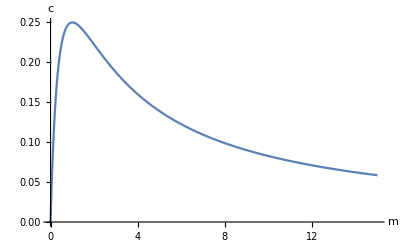

```mathematica
Plot[m/(1+m)/(1+m),{m,0,15},PlotRange->{0,All},AxesLabel->{m,c}]
```

### Test / usage example

```mathematica
params={Dm->1,Dc->1000,L->50};
```

```mathematica
initRun=runTwoComponentSim[
{f,-f},
params,
{5-4.5Cos[Pi#/L]&,1&},
1000
];
```

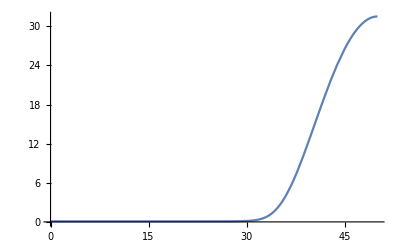

```mathematica
Plot[Evaluate[m[x,1000]/.initRun],{x,0,L/.params}]
```

```mathematica
fdSetup=setupFiniteDifferenceEqs[f,200];
```

```mathematica
testSol=Block[{m},FindRoot[
fdSetup["Eqs"]/.Join[{n->6},params],
getInitGuess[fdSetup,params,initRun,1000]
]
];//AbsoluteTiming
```

{0.056729,Null}

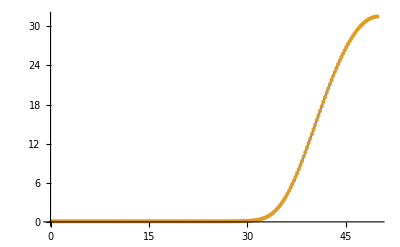

```mathematica
ListPlot[Transpose/@{
{x,m[x,1000]/.initRun}/.x->(L/.params) fdSetup["UnitGrid"],
{(L/.params) fdSetup["UnitGrid"],fdSetup["mVec"]/.testSol}
},
PlotRange->All,
Joined->{True,False}
]
```

### η_stat(M) at D_c=10000

```mathematica
params={Dm->1,Dc->10000,L->100};
```

#### Init

```mathematica
initRun=runTwoComponentSim[
{f,-f},
params,
{1-0.5Cos[Pi#/L]&,0.25&},
10000
];
```

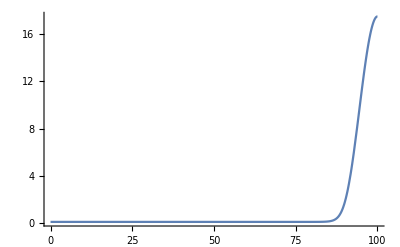

```mathematica
Plot[Evaluate[m[x,10000]/.initRun],{x,0,100},PlotRange->All]
```

```mathematica
fdSetup=setupFiniteDifferenceEqs[f,200];
```

```mathematica
testSol=Block[{m},FindRoot[
fdSetup["Eqs"]/.Join[{n->1.25},params],
getInitGuess[fdSetup,params,initRun,10000]
]
];//AbsoluteTiming
```

{0.060963,Null}

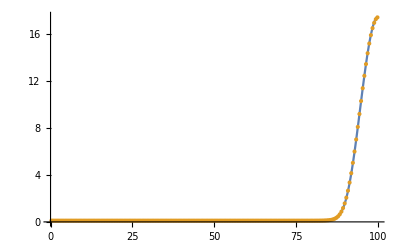

```mathematica
ListPlot[Transpose/@{
{x,m[x,10000]/.initRun}/.x->(L/.params) fdSetup["UnitGrid"],
{(L/.params) fdSetup["UnitGrid"],fdSetup["mVec"]/.testSol}
},
PlotRange->All,
Joined->{True,False}
]
```

#### n̄-sweep

We use the average mass n̄ as control paramater. Because, the lower plateau density n_- is neglgible, M≈L n̄

```mathematica
Off[FindRoot::lstol]
```

```mathematica
sweepN=Block[{m,sol,prevSol=testSol,evsN,evsA},
Table[
sol=FindRoot[
fdSetup["Eqs"]/.Join[{n->nIter},params],
prevSol/.Rule->List
];

prevSol=sol;
{
nIter,sol
},
{nIter,10^Range[Log10@1.25,Log10@100,0.025]}
]];
```

Profile at final sweep point (n̄=100)

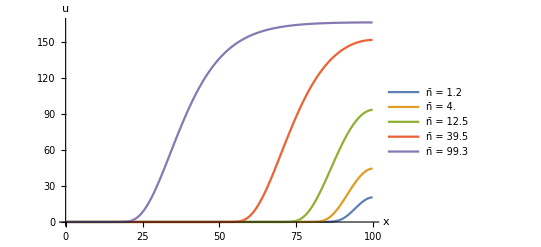

```mathematica
ListLinePlot[Transpose@{(L/.params) fdSetup["UnitGrid"],fdSetup["mVec"]/.sweepN[[#,2]]}&/@{4,21,41,61,-1},
PlotRange->All,
AxesLabel->{x,u},
BaseStyle->14,
PlotLegends->{Row[{"n̄ = ",Round[sweepN[[#,1]],0.1]}]&/@{1,21,41,61,-1}}
]
```

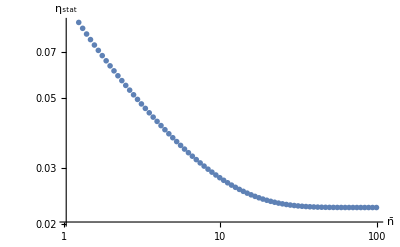

```mathematica
ListLogLogPlot[{
{#[[1]],η/.#[[2]]}&/@sweepN
},
PlotMarkers->{{Graphics[Disk[]],0.025}},
AxesLabel->{OverBar[n],Subscript[η, "stat"]},
BaseStyle->14
]
```

### Exponential approach to η_∞ in mesa regime

#### Determining η_∞

```mathematica
FBSNCanalytic=Solve[(1+m)(η-d m)==m/(1+m),m];
```

```mathematica
turnoverAnalytic=Integrate[(1+m)(η-d m)-m/(1+m),{m,mm,mp},Assumptions->mm>0&&mp>0&&mm<mp];
```

```mathematica
getEtaInfty[Dc_,initGuess_]:=η0/.FindRoot[turnoverAnalytic/.Thread[{mm,mp}->MinMax@Re[m/.FBSNCanalytic/.{d->1/Dc,η->η0}]]/.{d->1/Dc,η->η0},
{η0,initGuess},
Evaluated->False
]
```

```mathematica
ηInfty=getEtaInfty[10000,0.06]
```

0.0225714

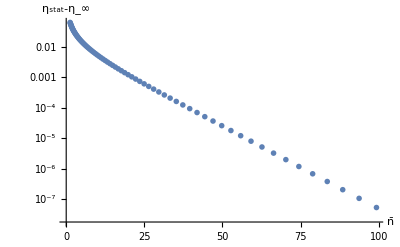

```mathematica
ListLogPlot[{#[[1]],η-ηInfty/.#[[2]]}&/@sweepN,PlotRange->All,
PlotMarkers->{{Graphics[Disk[]],0.03}},
AxesLabel->{OverBar[n],Subscript[η, "stat"]-Subscript[η, ∞]},
BaseStyle->14
]
```

#### ∂_n η_stat

Central differences on the logarithmic n̄ axis

```mathematica
With[{
lognList=Log10[sweepN[[All,1]]],
centralDifferences=Differences[η/.sweepN[[All,2]],1,2]
},
detadnTable=Transpose@{sweepN[[2;;-2,1]],(1/Log[10]/sweepN[[2;;-2,1]])centralDifferences/Differences[lognList,1,2]}
];
```

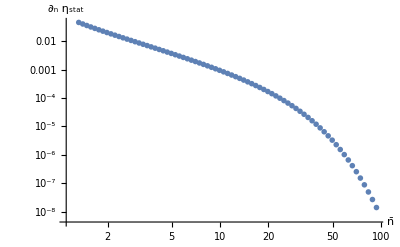

```mathematica
ListLogLogPlot[Abs@detadnTable,PlotMarkers->{{Graphics[Disk[]],0.025}},
AxesLabel->{"n̄","∂_n η_stat"},BaseStyle->14
]
```

Coarsening master curve.

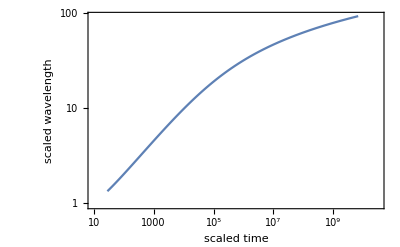

```mathematica
ListLogLogPlot[
Transpose@{-detadnTable[[All,1]]/detadnTable[[All,2]],detadnTable[[All,1]]},
Joined->True,
Frame->True,
FrameLabel->{"scaled time","scaled wavelength"},
BaseStyle->14,
RotateLabel->True,
PlotRange->{{10,10^10.5},All}
]
```